449 Final 
Megan Tabbutt
5/11/18

```mathematica
Import["/Users/megantabbutt/Desktop/Quantum/Defs/448defs.m"]
```

Notes about Citation Notation: 

T.11 = Townsend Ch 11 
All equation numbers not noted as a specific text are townsend: (11.24) = townsend equation 11.24 vs (Griffiths 11.24)

## 2) A Rb atom in the 50s state is in an electric field ℰ. In zero field the 50 p state has slightly higher energy than the 50 s, and the 49 p has slightly lower energy by very nearly the same amount, Δ. The radial integral ( ). Find the change in the 50 s energy as a function of electric field, for small fields.

Nondegenerate perturbation theory (Townsend Ch 11) 

“First order energy shift” - (A section in T.11)

 E_n^(1) = ϕ_n^(0)H_1 ϕ_n^(0) 					(11.15)

Electric field E --> H_1 = e Z ℰ 						(class notes and midterm 2) 


(E_(50s))^(1) = (ϕ_(50s))^(0)H_1(ϕ_(50s))^(0) = (E_(50s))^(1) = (ϕ_(50s))^(0)e Z ℰ(ϕ_(50s))^(0)

But the s state is spherically symmetric and the Z operator can be expressed in terms of Ylm’s that will have a theta dependance so this is zero, as well z is odd but the matrix elements are the same so it will evaluate to zero. 

“second order energy shift” - (A section in T.11)

E_n^(2) = ϕ_n^(0)Hϕ_n^(1)						(11.25)

E_n^(2) = ϕ_n^(0)Hϕ_n^(1)	 =  SUM[ (|ϕ_k^(0)Hϕ_n^(0)|^2)/(E_n^(0)- E_k^(0))] for k =! n  		(11.25)

Plug the 50s, 50p, 49p for n and k 

(E_(50s))^(2) = (|(ϕ_(50p))^(0)H(ϕ_(50s))^(0)|^2)/((E_(50s))^(0)- (E_(50p))^(0))+(|(ϕ_(49p))^(0)H(ϕ_(50s))^(0)|^2)/((E_(50s))^(0)- (E_(49p))^(0)) , H = e Z ℰ  ( as previously stated)

z = Y_10 2 r Sqrt[π/3]			(Wikipedia: Table of spherical harmonics)

(E_(50s))^(2) = (|(ϕ_(50p))^(0)H(ϕ_(50s))^(0)|^2)/((E_(50s))^(0)- (E_(50p))^(0))+(|(ϕ_(49p))^(0)H(ϕ_(50s))^(0)|^2)/((E_(50s))^(0)- (E_(49p))^(0)) 

(E_(50s))^(2) = (|(ϕ_(50p))^(0)e Y_10 2 r Sqrt[π/3] ℰ(ϕ_(50s))^(0)|^2)/-Δ+(|(ϕ_(49p))^(0)e Y_10 2 r Sqrt[π/3] ℰ(ϕ_(50s))^(0)|^2)/Δ 

(E_(50s))^(2) = 4 e^2 ℰ^2 π/3( (|(ϕ_(50p))^(0)Y_10 r  (ϕ_(50s))^(0)|^2)/-Δ+(|(ϕ_(49p))^(0) Y_10 r(ϕ_(50s))^(0)|^2)/Δ )

(E_(50s))^(2) = (4 e^2 ℰ^2 π/3)/Δ( |(ϕ_(49p))^(0) Y_10 r(ϕ_(50s))^(0)|^2 -|(ϕ_(50p))^(0)Y_10 r  (ϕ_(50s))^(0)|^2)

∫ⅆ rP_(50s)(r)rP_np(r) = n^2 a 				(use Griffiths notation, a = a0)

(E_(50s))^(2) = (4 e^2 ℰ^2 π/3)/Δ( |(ϕ_(49p))^(0) Y_10 r(ϕ_(50s))^(0)|^2 -|(ϕ_(50p))^(0)Y_10 r  (ϕ_(50s))^(0)|^2)

```mathematica
(Integrate[(49^2*a)SphericalHarmonicY[1, -1, θ, ϕ]*SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}]+Integrate[(49^2*a)SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}]+Integrate[(49^2*a)SphericalHarmonicY[1, 1, θ, ϕ]*SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}])^2
```

(5764801 a^2)/(4 π)

```mathematica
(Integrate[(50^2*a)SphericalHarmonicY[1, -1, θ, ϕ]*SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}]+Integrate[(50^2*a)SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}]+Integrate[(50^2*a)SphericalHarmonicY[1, 1, θ, ϕ]*SphericalHarmonicY[1, 0, θ, ϕ]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}])^2
```

(1562500 a^2)/π

(E_(50s))^(2) =  (4 e^2 ℰ^2 π/3)/Δ( (5764801 a^2)/(4 π) -(1562500 a^2)/π)

```mathematica
(5764801 a^2)/(4 π) - (1562500 a^2)/π
```

-(485199 a^2)/(4 π)

```mathematica
-(485199 a^2)/(4 π)* (4 e^2 ℰ^2 π/3)/Δ//N
```

-(161733. a^2 e^2 ℰ^2)/Δ

(E_(50s))^(2) = -(161733. a^2 e^2 ℰ^2)/Δ,  
a = bohr radius, e = electron charge, ℰ is the electric field, and (E_(50s))^(2) is the second order energy shift to the 50s state.

(E_(50s))^(2) = -(161733. a^2 e^2 ℰ^2)/Δ

Citation Summary: Townsend, Wikipedia (Ylms), Walker Perturbation Thoery Notebook

## 3) Rb

a) calculate the g-factor, g_j , for the Zeeman Effect  in the 5 P_(3/2) state of Rb.

(P) L = 1 			(Griffiths 5.2.2)
 s = 1/2 
 n = 5 (given) 
 j = 3/2 
 
 Follow procedure on Hmwk 4, #6 solutions 
 
Clebsch Gordon:		j m_j = (C_(l m_l s m_s))^(j m_j)m_l m_s 

3/2 3/2 = (C_(1 11/2 1/2))^(3/2 3/2)1 1/2 = 1 1 1/2 (see CG below)

```mathematica
ClebschGordan[{1, 1},{1/2, 1/2},{3/2, 3/2}]
```

1

⟨L_z+2 S_z⟩= g_j⟨J_z⟩

(1+2 1/2)= g_j⟨J_z⟩ = g_j 3/2

2 = g_j 3/2 --> 	g_j= 4/3

g_j= 4/3

b) The 5 P_(3/2) state has a hyperfine structure due to the interaction of the electron with the nucleus, whose spin in i = 3/2. Let F = J + I be the total ang mom operator. What are the possible values of the corresponding ang mom quantum number f?

F = J + I 

J = 3/2 , I = 3/2		

|j-i| ≤ f ≤ |j +i|			(Steck: Rubidium 87 D Line Data)(14)

f = (3/2 + 3/2), (3/2 + 1/2), (3/2 - 1/2), (3/2 -3/2)

f = 3, 2, 1, 0

f = 3, 2, 1, 0

c) Find the g factor ( ie: E = g_f μ_B Bm_f) for the 5 P_(3/2)  f = 3 level. Assume the relevant Zeeman Hamiltonian is V = g_j μ_B J \dot B

This formula can be found in the paper: Steck: Rubidium 87 D Line Data, in addition it is also in Woodgate in a slightly different  form. As well we will neglect the gi term as it is smaller than gj by a factor of the mass ratio of the proton to electron, this is quoted to have a correction at the .1% level in Steck, so we will neglect gi here. 

For, 

E = g_f μ_B Bm_f,  

V = g_j μ_B J \dot B:


g_f = g_J (f(f+1) - I (I+1) + J(J+1))/(2 f(f+1)) ,	 	
assuming g_I is much smaller than g_f, which IS true: citation: (Steck: Rubidium 87 D Line Data) (23)

```mathematica
Subscript[g, f] = Subscript[g, J] (f(f+1) - II (II+1) + J(J+1))/(2 f(f+1))/. {Subscript[g, J] -> 4/3, f -> 3, II -> 3/2, J -> 3/2}
```

2/3

g_f  = 2/3

Citation Summary: Walker hmwk #4 solutions, Townsend ch 11, Wikipedia: total ang mom quantum number, Steck: Rubidium 87 D Line Data, Woodgate: Elementary Atomic Structure

## 4) Consider the interaction of a 2-level system {g, e} with an oscillating field: H = ℏ ω0 |e⟩⟨e| + V(t) = ℏ ω0 |e⟩⟨e| + ℏ ωr Cos[ω t]|e⟩⟨g|+ ℏ ωr Cos[ω t]|g⟩⟨e|. Let the Rabi frequency ωr be small compared to the detuning ω - ω0, so that the probability of finding the system in the excited state is small, ⟨g|ψ⟩≈ 1. You can make the rotating wave approximation to simplify your work.

a) Find the probability of finding the system in state e in steady state.

Follow time dependent perturbations notebook: (nb) 

Make H = Ha + Ht, where Ha is the time independent part

Ha = ℏ ω0 |e⟩⟨e| 
Ht = ℏ ωr Cos[ω t]|e⟩⟨g|+ ℏ ωr Cos[ω t]|g⟩⟨e| 

Assume this form: ψ=c_g ⅇ^(-ⅈ E_g t/ℏ)g+∑_(k≠g) c_k ⅇ^(-ⅈ E_k t/ℏ)k 		(nb) 

So, ψ=c_g ⅇ^(-ⅈ ω0 t)g+c_e ⅇ^(-ⅈ ω0t)e 

But, ⟨g|ψ⟩≈ 1		g c_g ⅇ^-ⅈω0t g = 1   --> c_g ⅇ^-ⅈω0t = 1

So,		 ψ = g + c_e ⅇ^(-ⅈ ω0 t)e

We first assume that the effect of the perturbation is small, so that |c_g|≈1 and c_e≪1.  (nb)

ⅈ ℏ eψ̇ =eHaψ+eV(t)ψ=eψ+eVψ

ⅈ ℏ (d/dt c_e- ⅈ ω0 c_e)ⅇ^(-ⅈ ω0 t)  = ℏ ω0 c_e ⅇ^(-ⅈ ω0 t) + ⟨e|V |g⟩

d/dt c_e= ⟨e|V |g⟩/(ⅈ ℏ ⅇ^(-ⅈ ω0 t))

⟨e|V |g⟩ = ⟨e|(ℏ ωr Cos[ω t]|e⟩⟨g|+ℏ ωr Cos[ω t]|g⟩⟨e|)|g⟩ 
= ⟨e|(ℏ ωr Cos[ω t]|e⟩

d/dt c_e= ⟨e|(ℏ ωr Cos[ω t]|e⟩/(ⅈ ℏ ⅇ^(-ⅈ ω0 t))

d/dt c_e= (ωr Cos[ω t])/(ⅈ  ⅇ^(-ⅈ ω0 t))

d/dt c_e=  -ⅈ ωr 1/2(ⅇ^(ⅈ ωt)+ ⅇ^(-ⅈ ωt))ⅇ^(ⅈ ω0 t)

Rotating Wave Approx: throw out ω + ω0 terms 

d/dt c_e=  -ⅈ ωr 1/2 ⅇ^(ⅈ (ω -ω0)t)  =  -ⅈ ωr 1/2 ⅇ^(-ⅈ (ω -ω0)t)


c_e= ∫_0^t ⅆt' -ⅈ ωr 1/2 ⅇ^(-ⅈ (ω -ω0)t')

```mathematica
Integrate[-ⅈ ωr 1/2 ⅇ^(-ⅈ (ω -ω0)t), {t, 0, T}]
```

-((1-ⅇ^(-ⅈ T (ω-ω0))) ωr)/(2 (ω-ω0))

c_e= -((1-ⅇ^(-ⅈ t (ω-ω0))) ωr)/(2 (ω-ω0))

```mathematica
(-((1-ⅇ^(-ⅈ t (ω-ω0))) ωr)/(2 (ω-ω0)))*(-((1-ⅇ^(ⅈ t (ω-ω0))) ωr)/(2 (ω-ω0)))//FullSimplify
```

(ωr^2 Sin[1/2 t (ω-ω0)]^2)/(ω-ω0)^2

|c_e|^2= (ωr^2 Sin[1/2 t (ω-ω0)]^2)/(ω-ω0)^2

Time average: |c_e|^2 ≃ωr^2/(2(ω-ω0)^2)

the probability of finding the system in state e in steady state: |c_e|^2 ≃ωr^2/(2(ω-ω0)^2)

b) Calculate <V>.

< V> = ⟨ψ|V |ψ⟩

< V> = (g+ c_e^*ⅇ^(ⅈ ω0 t)e)(ℏ ωr Cos[ω t]|e⟩⟨g|+ℏ ωr Cos[ω t]|g⟩⟨e|) (g + c_e ⅇ^(-ⅈ ω0 t)e)
= (g+ c_e^*ⅇ^(ⅈ ω0 t)e)ℏ ωr Cos[ω t]|e⟩ + c_e ⅇ^(-ⅈ ω0 t) ℏ ωr Cos[ω t]|g⟩
= c_e^*ⅇ^(ⅈ ω0 t) ℏ ωr Cos[ω t]+ c_e ⅇ^(-ⅈ ω0 t) ℏ ωr Cos[ω t]

```mathematica
-((1-ⅇ^(ⅈ t (ω-ω0))) ωr)/(2 (ω-ω0))ⅇ^(ⅈ ω0 t) ℏ ωr Cos[ω t]+ -((1-ⅇ^(-ⅈ t (ω-ω0))) ωr)/(2 (ω-ω0))ⅇ^(-ⅈ ω0 t) ℏ ωr Cos[ω t] //FullSimplify
```

(ωr^2 ℏ Cos[t ω] (Cos[t ω]-Cos[t ω0]))/(ω-ω0)

< V> = = (ωr^2 ℏ Cos[t ω] (Cos[t ω]-Cos[t ω0]))/(ω-ω0)

< V>  = (ωr^2 ℏ Cos[t ω] (Cos[t ω]-Cos[t ω0]))/(ω-ω0)

Sources: Time dependant perturbation theory notebook

## 5)Use a variational He wavefunction to calculate < r_1^2+r_2^2> for the ground state. Use this to get a numerical value for the diamagnetic energy shift (Hdia = (e^2 B^2)/(2 m c^2)1/4<x^2+y^2>) in the earth’s magnetic field (.5 gauss). Hint for dealing with units: B =(μ_B B)/μ_B = (μ_B B)/((e ℏ)/(2 m c)) .

Following He1s2s notebook, and li project solutions:

```mathematica
Subscript[P, n_][r_]:=√2 Subscript[P, n,0][2r]
```

```mathematica
V[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[Subscript[P, n1][r1]Subscript[P, n3][r1]Min[1/r2,1/r1]Subscript[P, n2][r2]Subscript[P, n4][r2],{r2,0,∞},{r1,0,∞},AccuracyGoal->7];E0[{n1_,n2_}]:=-2/n1^2+-2/n2^2
```

```mathematica
st=DeleteDuplicates[Table[{{1,i},{i,1}},{i,4}]~Flatten~1]
```

{{1,1},{1,2},{2,1},{1,3},{3,1},{1,4},{4,1}}

```mathematica
Quiet[Vmat=Table[V[st⟦i⟧,st⟦j⟧],{i,Length[st]},{j,Length[st]}]];
```

```mathematica
H=DiagonalMatrix[E0/@st]+Vmat;
```

```mathematica
H//MatrixForm
```

(-2.75 | -0.17871 | -0.17871 | 0.0879189 | 0.0879189 | -0.0552137 | -0.0552137
-0.17871 | -2.08025 | 0.0438957 | -0.101053 | -0.0224458 | 0.0574314 | 0.0142681
-0.17871 | 0.0438957 | -2.08025 | -0.0224458 | -0.101053 | 0.0142681 | 0.0574314
0.0879189 | -0.101053 | -0.0224458 | -2.02325 | 0.0115356 | -0.0576774 | -0.007345
0.0879189 | -0.0224458 | -0.101053 | 0.0115356 | -2.02325 | -0.007345 | -0.0576774
-0.0552137 | 0.0574314 | 0.0142681 | -0.0576774 | -0.007345 | -2.00973 | 0.00467927
-0.0552137 | 0.0142681 | 0.0574314 | -0.007345 | -0.0576774 | 0.00467927 | -2.00973)

```mathematica
eval=Eigenvalues[H]⟦;;3⟧;eval
```

{-2.84138,-2.17096,-2.1366}

```mathematica
evec=Eigenvectors[H];evec//MF
```

(0.954 | 0.198 | 0.198 | -0.0685 | -0.0685 | 0.0407 | 0.0407
1.3×10^-7 | 0.62 | -0.62 | 0.334 | -0.334 | -0.0634 | 0.0634
0.116 | -0.469 | -0.469 | -0.521 | -0.521 | 0.0467 | 0.0467
-1.02×10^-7 | 0.172 | -0.172 | -0.421 | 0.421 | -0.541 | 0.541
-0.0628 | 0.198 | 0.198 | -0.242 | -0.242 | -0.633 | -0.633
-4.38×10^-8 | 0.294 | -0.294 | -0.459 | 0.459 | 0.451 | -0.451
0.271 | -0.449 | -0.449 | 0.407 | 0.407 | -0.31 | -0.31)

Previous was for what we did in class, but now we want it to be: < r_1^2+r_2^2>

```mathematica
Vm[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[Subscript[P, n1][r1]Subscript[P, n3][r1](r1^2+r2^2)Subscript[P, n2][r2]Subscript[P, n4][r2],{r2,0,∞},{r1,0,∞},AccuracyGoal->7];
```

```mathematica
Quiet[Vmatm=Table[Vm[st⟦i⟧,st⟦j⟧],{i,Length[st]},{j,Length[st]}]];
```

```mathematica
Hm=DiagonalMatrix[E0/@st]+Vmatm;
```

```mathematica
evec⟦1⟧.Vmatm.evec⟦1⟧
```

3.10492

Use first order PT theory: (See #2) (townsend ch 11)

 E_n^(1) = ϕ_n^(0)H_1 ϕ_n^(0) 	
 
  E_0^(1) = ϕ_0^(0) (e^2 B^2)/(2 m c^2)1/4<x^2+y^2>ϕ_0^(0) 	
 
  E_0^(1) =(e^2 B^2)/(2 m c^2)1/4 ϕ_0^(0) <x^2+y^2>ϕ_0^(0) 	
 
 ϕ_0^(0) = 1s1s state 
 
 x^2+ y^2+z^2 = r^2 -->	x^2+ y^2= r^2-z^2 
 
   E_0^(1) =(e^2 B^2)/(2 m c^2)1/4 1s1s r^2-z^2 1s1s 	
  
  With, r^2= r1^2+r2^2 etc:
  
   E_0^(1) =(e^2 B^2)/(2 m c^2)1/4 1s1s r1^2+r2^2 -(z1^2+z2^2)1s1s 	
  
 Spherical coordinates: z = rCos[θ]

   E_0^(1) =(e^2 B^2)/(2 m c^2)1/4 1s1s r1^2+r2^2 -((r1Cos[θ1])^2+((r2Cos[θ2])^2)^)1s1s

```mathematica
pintegrand = Subscript[P, n1][r1]*Subscript[P, n3][r1]*Subscript[P, n2][r2]*Subscript[P, n4][r2]
Yintegrand = SphericalHarmonicY[0, 0, θ1, ϕ1]*SphericalHarmonicY[0, 0, θ2, ϕ2]*SphericalHarmonicY[0, 0, θ1, ϕ1]*SphericalHarmonicY[0, 0, θ2, ϕ2]
Jacobians = Sin[θ1]*Sin[θ2]
dia = r1^2+r2^2 -r1^2 Cos[θ1]^2-r2^2 Cos[θ2]^2

Vdia[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[pintegrand*Yintegrand*Jacobians*dia,{r2,0,∞},{r1,0,∞},{θ1,0,π},{θ2,0,π}, {ϕ1,0,2π},{ϕ2,0,2π}, AccuracyGoal->7]
```

(1024 ⅇ^(-(2 r1)/n1-(2 r1)/n3-(2 r2)/n2-(2 r2)/n4) r1^2 r2^2 HypergeometricU[1-n1,2,(4 r1)/n1] HypergeometricU[1-n2,2,(4 r2)/n2] HypergeometricU[1-n3,2,(4 r1)/n3] HypergeometricU[1-n4,2,(4 r2)/n4])/(n1 n2 n3 n4 √(n1^2 Gamma[n1] Gamma[1+n1]) √(n2^2 Gamma[n2] Gamma[1+n2]) √(n3^2 Gamma[n3] Gamma[1+n3]) √(n4^2 Gamma[n4] Gamma[1+n4]))

1/(16 π^2)

Sin[θ1] Sin[θ2]

r1^2+r2^2-r1^2 Cos[θ1]^2-r2^2 Cos[θ2]^2

```mathematica
Vdia[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[Integrate[Subscript[P, n1][r1]Subscript[P, n3][r1]SphericalHarmonicY[0, 0, θ1, ϕ1]SphericalHarmonicY[0, 0, θ2, ϕ2](r1^2+r2^2 -((r1*Cos[θ1])^2+(r2*Cos[θ2])^2))Subscript[P, n2][r2]Subscript[P, n4][r2]SphericalHarmonicY[0, 0, θ1, ϕ1]SphericalHarmonicY[0, 0, θ2, ϕ2]Sin[θ1]Sin[θ2],{θ1,0,π},{θ2,0,π}, {ϕ1,0,2π},{ϕ2,0,2π}],{r2,0,∞},{r1,0,∞}, AccuracyGoal->7]
```

```mathematica
Vmatdia=Table[Vdia[st⟦i⟧,st⟦j⟧],{i,Length[st]},{j,Length[st]}];
```

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (32 ⅇ^(-(8 r1)/3-4 r2) r1^2 (6-8 r1+(16 r1^2)/9) r2^2 (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (32 ⅇ^(-4 r1-(8 r2)/3) r1^2 r2^2 (6-8 r2+(16 r2^2)/9) (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (64 ⅇ^(-4 r1-4 r2) r1^2 r2^2 (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (32 ⅇ^(-(8 r1)/3-4 r2) r1^2 (6-8 r1+(16 r1^2)/9) r2^2 (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (32 ⅇ^(-4 r1-(8 r2)/3) r1^2 r2^2 (6-8 r2+(16 r2^2)/9) (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (64 ⅇ^(-4 r1-4 r2) r1^2 r2^2 (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (32 ⅇ^(-(8 r1)/3-4 r2) r1^2 (6-8 r1+(16 r1^2)/9) r2^2 (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (32 ⅇ^(-4 r1-(8 r2)/3) r1^2 r2^2 (6-8 r2+(16 r2^2)/9) (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (64 ⅇ^(-4 r1-4 r2) r1^2 r2^2 (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (64\ SuperscriptBox[ⅇ, -4\ r1 - 4\ r2]\ SuperscriptBox[r1, 2]\ SuperscriptBox[r2, 2]\ (SuperscriptBox[r1, 2] + SuperscriptBox[r2, 2] - SuperscriptBox[r1, 2]\ SuperscriptBox[Cos[θ1], 2] - SuperscriptBox[(SuperscriptBox[r2, 2]\ SuperscriptBox[Cos[θ2], 2]), Null]))/π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}, {∞, 0.}, {0, 3.14159}, {0, 3.14159}, {0, 6.28319}, {0, 6.28319}}.

NIntegrate::inumr: The integrand (32 ⅇ^(-4 r1-(8 r2)/3) r1^2 r2^2 (6-8 r2+(16 r2^2)/9) (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

NIntegrate::inumr: The integrand (32 ⅇ^(-(8 r1)/3-4 r2) r1^2 (6-8 r1+(16 r1^2)/9) r2^2 (r1^2+r2^2-r1^2 Cos[θ1]^2-(r2^2 Cos[θ2]^2)^Null))/(9 √3 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.},{∞,0.},{0,3.14159},{0,3.14159},{0,6.28319},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Hdia=DiagonalMatrix[E0/@st]+Vmatdia;
```

```mathematica
evec⟦1⟧.Vmatdia.evec⟦1⟧
```

2.06995

2.06995 (a0^2), Energy in Hdia is in mass units so need to multiply by c^2 to get to energy

```mathematica
ee = 1.602*10^-19; B = .5*10^-4; m = 9.109*10^-31; cc = 3.0*10^8; a0 = 5.29*10^-11;
 EEEEE=(ee^2 B^2)/(2 m)1/4*2.06995((a0))^2
```

5.10006×10^-38

5.10006×10^-38 Joules

Citations: He1s2s notebook, li project solution, townsend ch 11

## 6) Consider a repulsive potential such as V(r) = C/r^8. This mimics the potential seen by a Rb in collisions with He atoms.

a) Draw a realistic sketch of the zero-point radial wavefunction and from it deduce the sign of the scattering length.

Use code from homework 6 and the swave scattering notebook:

```mathematica
SE[e_]:=-1/2 p''[r]-(40/27.2)/(r)^8 p[r]== e p[r];
```

```mathematica
p0[r_]=NDSolve[{SE[0],p[1]==0,p'[1]==1},p[r],{r,0,2000}]⟦1,1,2⟧
```

NDSolve::mxst: Maximum number of 119314 steps reached at the point r == 0.0454214.

InterpolatingFunction[{{0.0454214, 2000.}}, <>][r]

```mathematica
NSolve[{p0[200]== c(200-a),p0'[200]==c },{c,a}]
```

{{c→0.931281,a→0.970839}}

```mathematica
4π (0.9708392505000866 .5292 Å)^2
```

3.31699 Å^2

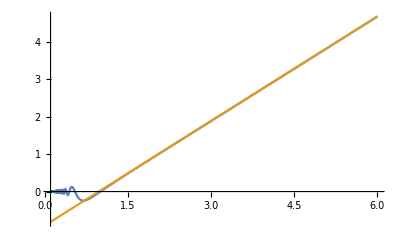

```mathematica
Plot[{p0[r],0.9312809160420462(r-0.9708392505000866)},{r,0.1,6}]
```

The Scattering length is positive

b) Calculate the zero energy cross section for Rb atoms scattering from He, where C = 40 eV Angstoms^8.

```mathematica
4π (0.9708392505000866 .5292 Å)^2
```

3.31699 Å^2

Scattering Cross Section: 3.31699 Å^2

Citation Summary:  swave scattering notebook and Hmwk #6 solutions